```mathematica
SSSS[a1_,b1_,c1_,r1_,a2_,b2_,c2_,r2_,a3_,b3_,c3_,r3_,a4_,b4_,c4_,r4_,s_]:=Module[{m,n,a,b,c,rr,s1,s2,s3,s4,rrr,A,B,C,D,E,F,aa,bb,cc},{jj,s1,s2,s3,s4}=2 IntegerDigits[s+15,2]-1;
m={{-2 a1+2 a2,-2 b1+2 b2,-2 c1+2 c2,-2 s1 r1+2 s2 r2,-a1^2+a2^2-b1^2+b2^2-c1^2+c2^2+r1^2-r2^2},{-2 a2+2 a3,-2 b2+2 b3,-2 c2+2 c3,-2 s2 r2+2 s3 r3,-a2^2+a3^2-b2^2+b3^2-c2^2+c3^2+r2^2-r3^2},{-2 a3+2 a4,-2 b3+2 b4,-2 c3+2 c4,-2 s3 r3+2 s4 r4,-a3^2+a4^2-b3^2+b4^2-c3^2+c4^2+r3^2-r4^2}};n=RowReduce[m];A=n[[1,5]];B=n[[1,4]];
C=n[[2,5]];D=n[[2,4]];E=n[[3,5]];F=n[[3,4]];
aa=B^2+D^2+F^2-1;
bb=-2 A B-2 C D-2 E F+2 a1 B+2 b1 D+2 c1 F-2 s1 r1;
cc=A^2+C^2+E^2-2 a1 A-2 b1 C-2 c1 E+a1^2+b1^2+c1^2-r1^2;
rr=Max[(-bb+Sqrt[bb^2-4 aa cc])/(2 aa),(-bb-Sqrt[bb^2-4 aa cc])/(2 aa)];a=A-B rr;
b=C-D rr;c=E-F rr;Return[{a,b,c,rr}]]
```

```mathematica
openCone[{{x1_,y1_,z1_},{x2_,y2_,z2_}},r_]:={CapForm[None],Tube[{{x1,y1,z1},{x2,y2,z2}},{r,0}]}
CP[a_,A_,x0_,B_,y0_,C_,z0_]:=Module[{D,z,aa,bb,cc},D=-A x0-B y0-C z0;aa=(A^2+B^2+C^2) Sin[a °]^2-C^2;bb=-2 C D;cc=-D^2;z=(-bb+√(bb^2-4 aa cc))/(2 aa);Return[{z,z Sin[a °]}]]
```

```mathematica
CS[a_,x1_,y1_,z1_,r1_]:=Module[{aa,bb,cc,z,s1},s1=1;aa=1-Sin[a °]^2;bb=-2 z1-2 s1 r1 Sin[a °];cc=x1^2+y1^2+z1^2-r1^2;z=Min[(-bb+√(bb^2-4 aa cc))/(2 aa),(-bb-√(bb^2-4 aa cc))/(2 aa)];Return[{0,0,z,z Sin[a °]}]]
SsCs1[x1_,y1_,z1_,r1_,x2_,y2_,z2_,r2_,x3_,y3_,z3_,r3_,a_]:=Module[{x,y,z,r},
nsol = NSolve[{(x-x1)^2+(y-y1)^2+(z-z1)^2 == (r+r1)^2,(x-x2)^2+(y-y2)^2+(z-z2)^2 == (r+r2)^2,(x-x3)^2+(y-y3)^2+(z-z3)^2 == (r+r3)^2,
r==z Sin[a °]-Cos[a °] √(x^2+y^2),
-10<=x<=10,
-10<=y<=10,
0<=z,
0<=r<=10},
{x,y,z,r}][[3]];
Return[{x/.nsol,y/.nsol,z/.nsol,r/.nsol}]]
```

```mathematica
ymin=0;
ymax=0;
```

```mathematica
ymax
```

0

```mathematica
CSLoop[a_,x0_,y0_,z0_, r0_, n_] :=
Module[{x,y,z,r,lst,x1,y1,z1,r1},
lst={};
x=x0;
y=y0;
z=z0;
r=r0;
For[i=0,i<n,i++,
{x1,y1,z1,r1}={x,y,z,r};
{x,y,z,r}=CS[a,x,y,z,r];
ymax=y;
lst=Append[lst,{Red,Sphere[{x,y,z},r]}];
lst = Join[lst, CSSLoop3[a,x,y,z,r,x1,y1,z1,r1]];
];
Print[lst];
Return[lst]
]
CSSLoop3[aa_,x0_,y0_,z0_,r0_,x1_,y1_,z1_,r1_] :=
Module[{a,m,b,h,x,lst,theta,nn,t, t2, s1,s2,s3,s4,s5,s6,s7,s8,s0},
lst={};
a=aa Degree;
m=r0*(Sec[a]+Tan[a])^2;
b=r0*(Sec[a]+Tan[a])^2/(1+Sec[a]+Tan[a])^2;
h=r0*((2+Cos[a]) (1+Sin[a]))/(2 (1+Cos[a]));
x=r0*1/2 √((1+Cos[a]-Tan[a/2])^2);
theta=2*ArcSin[1/(2+Cos[a])];
nn=Floor[2 Pi/theta];
For[j=0,j<nn,j++,
t=j*theta;
lst=Append[lst,{Blue,Sphere[{h*Sin[t],h*Cos[t],z0+x},b]}];
If[j<nn-1,t2=(j+1)*theta;
s1=SsCs1[h*Sin[t],h*Cos[t],z0+x,b,h*Sin[t2],h*Cos[t2],z0+x,b,x1,y1,z1,r1,aa];
s5=SsCs1[h*Sin[t],h*Cos[t],z0+x,b,h*Sin[t2],h*Cos[t2],z0+x,b,x0,y0,z0,r0,aa];
lst=Append[lst,{Blue,Sphere[{s1[[1]],s1[[2]],s1[[3]]},s1[[4]]]}];
lst=Append[lst,{Blue,Sphere[{s5[[1]],s5[[2]],s5[[3]]},s5[[4]]]}];
];
If[j==nn-1,t2=0;
s0=SSSS[h*Sin[t],h*Cos[t],z0+x,b,h*Sin[t2],h*Cos[t2],z0+x,b,x1,y1,z1,r1,x0,y0,z0,r0];
lst=Append[lst,{Blue,Sphere[{s0[[1]],s0[[2]],s0[[3]]},s0[[4]]]}];];
Print["hi"]
];
Return[lst]
]
```

```mathematica
Manipulate[Show[
Graphics3D[{Opacity[0.5],openCone[{{0,0,10},{0,0,0}},10*Tan[a Degree]]}],(*Plot3D[(-(-A x0-B y0-C z0)-A x-B y)/C,{x,-3,3},{y,-3,3},BoxRatios->{1,1,1}],*)Graphics3D[{Red,Sphere[{0,0,CP[a,A,x0,B,y0,C,z0][[1]]},CP[a,A,x0,B,y0,C,z0][[2]]]}],
Graphics3D[{ColorData[97][4],CSLoop[a,0,0,CP[a,A,x0,B,y0,C,z0][[1]],CP[a,A,x0,B,y0,C,z0][[2]],1]}],
Boxed->False,ViewPoint->Back,PlotRange->{All,All,{(2 z0+2 z0 Sin[a °]^2-√((-2 z0-2 z0 Sin[a °]^2)^2-4 (1-Sin[a °]^2) (z0^2-(z0 Sin[a °])^2)))/(2 (1-Sin[a °]^2))(1-Sin[a Degree]),z0-z0 Sin[a Degree]}},ImageSize->Large,PlotRange->{{0,0,0},{1,1,1}}
],{{a,25},0,90},{{A,0},-1,1},{{B,0},-1,1},{{C,1},-1,1},{x0,-10,10},{y0,-10,10},{{z0,10},-10,10}]
```

```mathematica
FullSimplify[(2 10+2 10 Sin[a °]^2-√((-2 10-2 10 Sin[a °]^2)^2-4 (1-Sin[a °]^2) (10^2-(10 Sin[a °])^2)))/(2 (1-Sin[a °]^2))(1-Sin[a Degree])]
```

-(5 (-3+Cos[2 a °]+4 √(Sin[a °]^2)))/(1+Sin[a °])

```mathematica
Export["animationcone.mp4",Manipulate[Show[

Graphics3D[{Opacity[0.5],openCone[{{0,0,10},{0,0,0}},10*Tan[a Degree]]}],(*Plot3D[(-(-A x0-B y0-C z0)-A x-B y)/C,{x,-3,3},{y,-3,3},BoxRatios->{1,1,1}],*)Graphics3D[{Red,Sphere[{0,0,CP[a,0,-10,0,-10,1,10][[1]]},CP[a,0,-10,0,-10,1,10][[2]]]}],
Graphics3D[{ColorData[97][4],CSLoop[a,0,0,CP[a,0,-10,0,-10,1,10][[1]],CP[a,0,-10,0,-10,1,10][[2]],1]}],
Boxed->False,ViewPoint->Back,PlotRange->{All,All,{(2 10+2 10 Sin[a °]^2-√((-2 10-2 10 Sin[a °]^2)^2-4 (1-Sin[a °]^2) (10^2-(10 Sin[a °])^2)))/(2 (1-Sin[a °]^2))(1-Sin[a Degree]),10(1- Sin[a Degree])}},ImageSize->Large,Background->RGBColor[1,242/255,204/255]
],{a,18,30,0.2}]]
```

animationcone.mp4

1

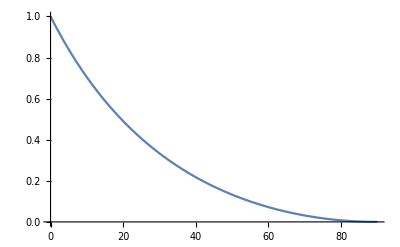

```mathematica
z=1
Plot[(2 z+2 z Sin[a °]^2-√((-2 z-2 z Sin[a °]^2)^2-4 (1-Sin[a °]^2) (z^2-(z Sin[a °])^2)))/(2 (1-Sin[a °]^2)),{a,0,90}]
```

```mathematica
Show[Graphics3D[{RGBColor[0, 1, 0],Sphere[{0,0,3.119068422774777},1.2287317706127319]}]]
```

-Graphics3D-

```mathematica
SsCs1[-0.2973848413688147,-0.10953526533675131,0.6382311750961249,0.11261653835473875,-0.29504667917491,0.11568567472338707,0.6382311750961249,0.11261653835473875,0,0,1.6781132644845937,0.9744853327039376,35.5]
```

{0.,0.,0.445136,0.258492}

```mathematica
ColorData[97][1]
```

RGBColor[0.368417, 0.506779, 0.709798]

```mathematica
c=ColorData["SouthwestColors"]
```

ColorDataFunction[…]

```mathematica
c[2]
```

RGBColor[0.35082, 0.595178, 0.853742]

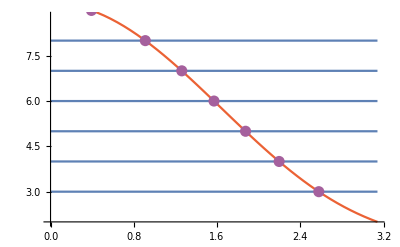

```mathematica
Show[Plot[{3,4,5,6,7,8,9},{hagherjcgvsgvhuksdf,0,Pi},PlotStyle->ColorData[97][1]],Plot[2Pi/(2*(ArcSin[1/(2+Cos[th])])),{th,0,Pi},PlotStyle->ColorData[97][4]],ListPlot[rootlst,PlotStyle->Directive[ColorData[97][9],PointSize[0.02]]],PlotRange->{{0,Pi},{2,8.8}},AxesOrigin->{0,2}]
```

```mathematica
rootlst = Table[{th/.FindRoot[2Pi/(2*(ArcSin[1/(2+Cos[th])]))==i,{th,2}],i},{i,3,9}]
```

{{2.57792,3},{2.19665,4},{1.87412,5},{1.5708,6},{1.2611,7},{0.910785,8},{0.392895,9}}

```mathematica
180*1.5707963267948963/Pi
```

90.

hi

hi

hi

«1 more identical outputs»